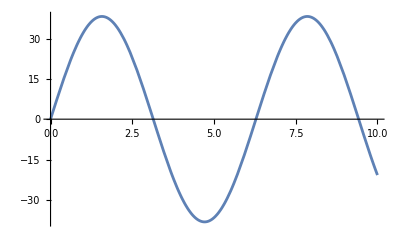

```mathematica
(*1st term *)
A=30;ω=1;
 y=(4A)/π Sum[1/(2*n-1)*Sin[(2*n-1)*ω*t],{n,1,1}];
Plot[y,{t,0,10}]
```

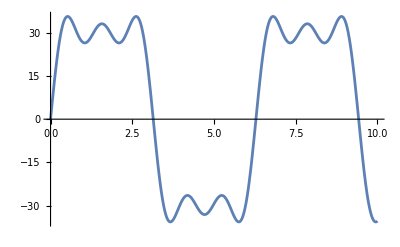

```mathematica
(*1st three terms *)
A=30;ω=1;
 y=(4A)/π Sum[1/(2*n-1)*Sin[(2*n-1)*ω*t],{n,1,3}];
Plot[y,{t,0,10}]
```

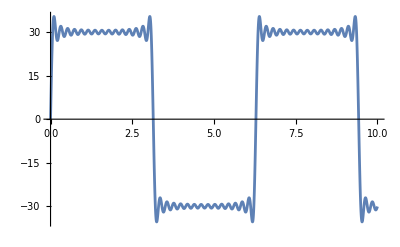

```mathematica
(*1st 15 terms *)
A=30;ω=1;
 y=(4A)/π Sum[1/(2*n-1)*Sin[(2*n-1)*ω*t],{n,1,15}];
Plot[y,{t,0,10}]
```

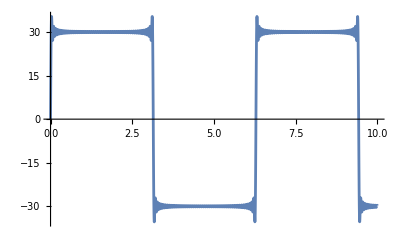

```mathematica
(*1st 50 terms *)
A=30;ω=1;
 y=(4A)/π Sum[1/(2*n-1)*Sin[(2*n-1)*ω*t],{n,1,50}];
Plot[y,{t,0,10}]
```

```mathematica
(*1st 1,5,50 terms *)
A=30;ω=1;
 y=(4A)/π Sum[1/(2*n-1)*Sin[(2*n-1)*ω*t],{n,1,{2,15}}];
Plot[y,{t,0,10}]
```